```mathematica
Clear[posfiles,positions]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Find out the max number of files there might be to import

[Header] and [Folder] should end in a ‘/’

```mathematica
Folder="RunData/";
Pos="Pos/Pos";
```

```mathematica
scale=150;
fps=15.;
```

```mathematica
maxRes=512;
```

```mathematica
animate=True;
```

## Import files

### Create file names

Position file names

```mathematica
posnum=Length[Sort[Import[Folder<>"Pos"]]];
If[posnum==$Failed,posnum=0,Null];
If[animate==True,Null,posnum=0]
Print["There are ", posnum, " files to import."]
```

There are 150 files to import.

```mathematica
posfiles={};
For[i=0,i<posnum,++i,AppendTo[posfiles,Folder<>Pos<>ToString[i]<>".csv"]]
```

#### Verlet list names

```mathematica
vernum=Length[Sort[Import[Folder<>"VLData"]]];
If[vernum==$Failed,vernum=0,Null];
If[animate==True,Null,vernum=0];
verfiles={};
For[i=0,i<vernum,++i,AppendTo[verfiles,Folder<>"VLData/VLData"<>ToString[i]<>"_0.csv"]]
```

### Import data

Get the positions

```mathematica
positions={};
For[i=1,i≤posnum,++i,If[FileExistsQ[posfiles⟦i⟧],AppendTo[positions,Import[posfiles⟦i⟧]],Null]]
onlyPositions=Map[#⟦1;;2⟧&,positions,{2}];
```

#### Get the verlet lists

```mathematica
verletLists={};
For[i=1,i≤vernum,++i,
If[FileExistsQ[verfiles⟦i⟧],AppendTo[verletLists,Import[verfiles⟦i⟧]],Null]]
(* C++ starts indexing with 0, Mathematica with 1, so we have to add 1 to all indices. *)
PreIncrement[verletLists];
```

## Create Plots

```mathematica
SaveDirectory=Folder<>"Output/";
If[posnum>0 ,Quiet[CreateDirectory[SaveDirectory]],Null];
```

### The lines (data, not graphics objects) for the verlet lists

```mathematica
verletLines=Function[{arg},
{pos,vl}=arg;
HH=1;
{pos⟦vl⟦1,HH⟧⟧,#}&/@pos⟦vl⟦1⟧⟦HH+1;;⟧⟧
]/@Transpose[{onlyPositions,verletLists}];
```

### Export positions

Position data: { x, y, sigma, theta, interaction, ‘color’ }

Color scaling function

```mathematica
bnds1d={{0,1},{-0.25,0.25}};
bnds2d={{0,1},{0,1}}; (* For now *)
bnds3d={{0,1},{0,1},{0,1}};
```

Shape definitions. Position data - { px, py, sg, th, it, “color data”}

```mathematica
dsk[tr_]:={col[tr⟦6⟧],Disk[{tr⟦1⟧,tr⟦2⟧},tr⟦3⟧]};
odsk[tr_]:={{col[tr⟦5⟧],{Disk[tr⟦1⟧,tr⟦2⟧]}},{Blue,Line[{tr[[1]],tr[[1]]+tr⟦2⟧,{Cos[tr[[3]]],Sin[tr[[3]]]}}]}};
ljdsk[tr_]:={{col[tr⟦6⟧],Circle[{tr⟦1⟧,tr⟦2⟧},tr⟦3⟧]},{col[tr⟦6⟧],Disk[{tr⟦1⟧,tr⟦2⟧},0.4tr⟦3⟧]}};
mvwll[tr_]:={Blue,Thickness[0.01],Line[{{tr⟦1⟧-tr⟦3⟧Cos[tr⟦4⟧],tr⟦2⟧-tr⟦3⟧Sin[tr⟦4⟧]},
{tr⟦1⟧+tr⟦3⟧Cos[tr⟦4⟧],tr⟦2⟧+tr⟦3⟧Sin[tr⟦4⟧]}}]}
```

#### Two and three dimensional circles/spheres

```mathematica
obj1d[tr_]:=Disk[{tr⟦1⟧,0},tr⟦2⟧]
obj2d[tr_]:=Disk[{tr⟦1⟧,tr⟦2⟧},tr⟦3⟧]
obj3d[tr_]:=Sphere[{tr⟦1⟧,tr⟦2⟧,tr⟦3⟧},tr⟦4⟧]
```

#### How many dimensions?

```mathematica
dim=Length[positions⟦1,1⟧]-1;
res={maxRes,maxRes};
```

#### Create and export movies

```mathematica
If[vernum==0,
(* If there are no verlet lists to show*)
Switch[dim,
1,
disks1d=Graphics[#,PlotRange->bnds1d,ImageSize->{1024,512}]&/@Map[obj1d,positions,{2}];Export[SaveDirectory<>"positions.avi",disks1d],
2,disks2d=Graphics[#,PlotRange->bnds2d,ImageSize->res]&/@Map[obj2d,positions,{2}];
Export[SaveDirectory<>"positions.avi",disks2d],
3,disks3d=Graphics3D[#,PlotRange->bnds3d,ImageSize->res]&/@Map[obj3d,positions,{2}];
Export[SaveDirectory<>"positions.avi",disks3d,"CompressionLevel"->0]
],
(* If we should show verlet lists *)
Switch[dim,
1,Null,
2,

verletdisks2=Show/@Transpose[{Graphics[obj2d/@#,PlotRange->bnds2d,ImageSize->res]&/@positions,
Graphics[{Red,Arrow[#]}]&/@verletLines}];

Export[SaveDirectory<>"positions.avi",verletdisks2,"CompressionLevel"->0],
3,Null
]
]
```

RunData/Output/positions.avi

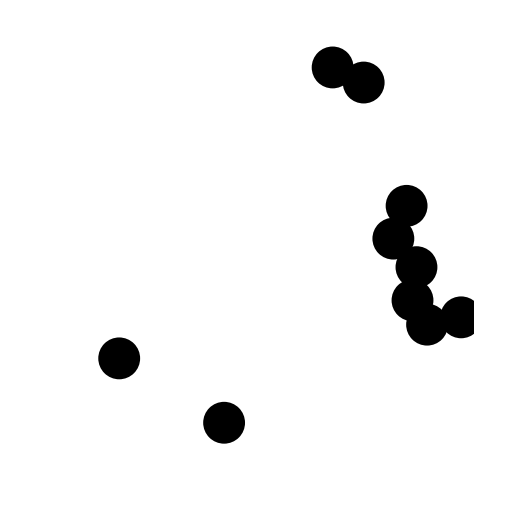
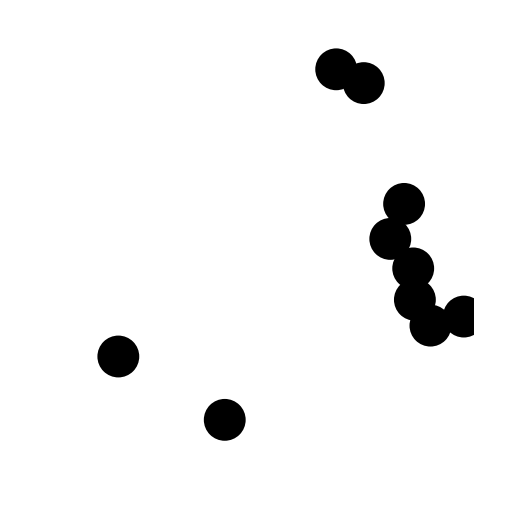
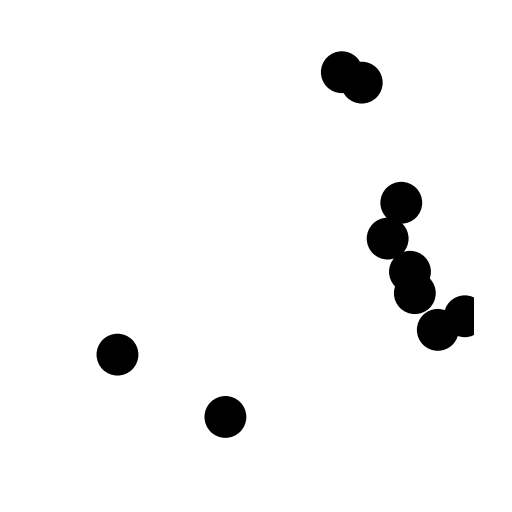
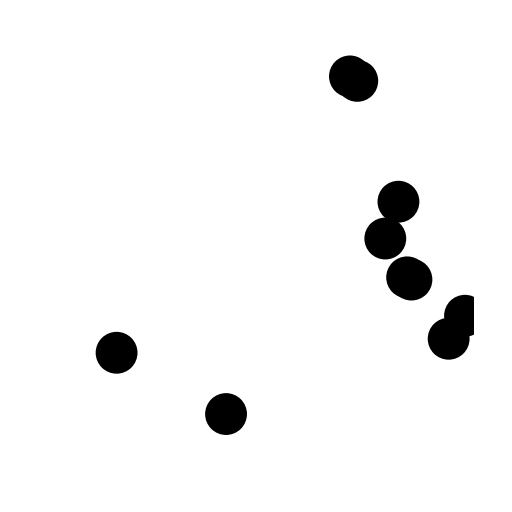
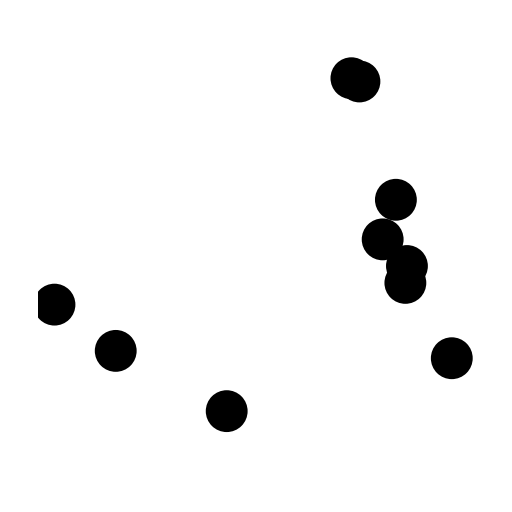
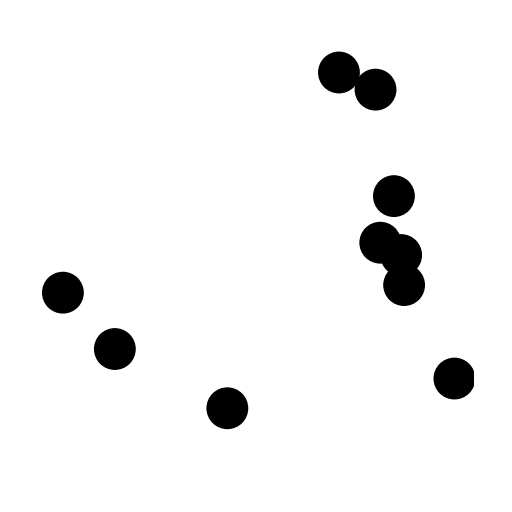
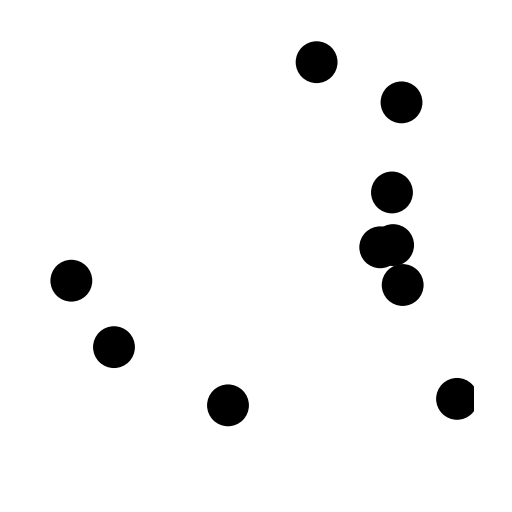
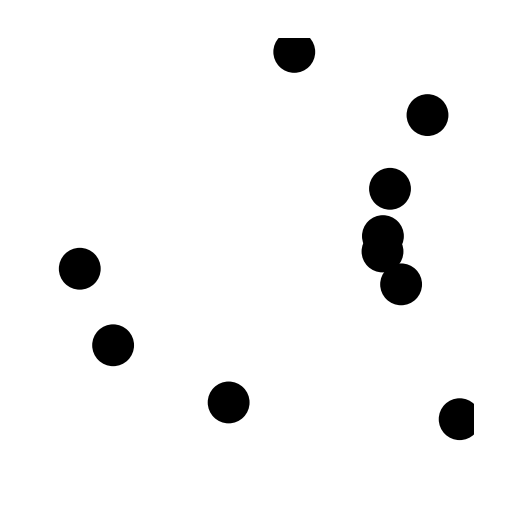
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
disks2d=Graphics[#,PlotRange->bnds2d,ImageSize->res]&/@Map[obj2d,positions,{2}]
```

```mathematica
Arrow
```

Arrow

```mathematica
Map[obj2d,positions,{2}]⟦1⟧//Graphics
```

-Graphics-

```mathematica
Show[#⟦1⟧,#⟦2⟧]&/@
Transpose[{Graphics[Map[obj2d,positions,{2}]],Graphics[{Red,Arrow[verletLines⟦1⟧]}]}]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose[-Graphics-]

```mathematica
Graphics[obj2d/@#]&/@positions;
Graphics[{Red,Arrow[#]}]&/@verletLines;
```

```mathematica
Show[Map[obj2d,positions,{2}]⟦1⟧//Graphics,{Red,Arrow[verletLines⟦1⟧]}//Graphics]
```

-Graphics-